Composición y visualización

Anteriormente se vio el uso de Framed para enmarcar algo que se muestra.

Genere un número y enmárquelo:

```mathematica
Framed[2^100]
```

1267650600228229401496703205376

Pueden darse opciones a Framed.

Especifique un color de fondo y un estilo para el marco:

```mathematica
Framed[2^100,Background->LightYellow,FrameStyle->LightGray]
```

1267650600228229401496703205376

Labeled sirve para poner etiquetas.

Agregue una etiqueta al número enmarcado:

```mathematica
Labeled[Framed[2^100],"a big number"]
```

1267650600228229401496703205376a big number

Ahora se agrega una etiqueta a un número que tiene ya un estilo de fondo amarillo:

```mathematica
Labeled[Style[2^100,Background->Yellow],"a big number"]
```

1267650600228229401496703205376a big number

Con esto se agrega un estilo a la etiqueta:

```mathematica
Labeled[Style[2^100,Background->Yellow],Style["a big number",Italic,Orange]]
```

1267650600228229401496703205376a big number

También puede usarse Labeled en gráficos.

Haga un diagrama circular con algunos de los sectores etiquetados:

```mathematica
PieChart[{Labeled[1,"one"],Labeled[2,"two"],Labeled[3,Red],Labeled[4,Orange],2,2}]
```

-Graphics-

Grafique puntos etiquetados:

```mathematica
ListPlot[{Labeled[1,"one"],Labeled[2,"two"],Labeled[3,Pink],Labeled[4,Yellow],5,6,7}]
```

-Graphics-

Grafique la lista de los primeros primos etiquetados con sus valores:

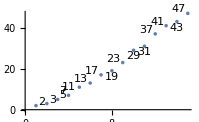

```mathematica
ListPlot[Table[Labeled[Prime[n],Prime[n]],{n,15}]]
```

Labeled señala alguna cosa poniéndole una etiqueta al lado. A veces se ve bien usar “líneas guía”, con unas líneas pequeñas apuntando a aquello a lo que se refieren. Para este propósito se usa Callout mejor que Labeled.

Callout crea “líneas guía” con líneas pequeñas:

```mathematica
ListPlot[Table[Callout[Prime[n],Prime[n]],{n,15}]]
```

-Graphics-

Hay una gran variedad de maneras de poner anotaciones en gráficos. Style inserta estilos directamente. Tooltip genera sugerencias interactivas que se hacen visibles cuando el ratón ronda sobre el gráfico. Legended coloca etiquetas en una leyenda al lado del gráfico.

Especifique estilos para los tres primeros sectores del diagrama circular:

```mathematica
PieChart[{Style[3,Red],Style[2,Green],Style[1,Yellow],1,2}]
```

-Graphics-

Use palabras y colores como leyendas para los sectores circulares:

```mathematica
PieChart[{Legended[1,"one"],Legended[2,"two"],Legended[3,Pink],Legended[4,Yellow],2,2}]
```

-Graphics-

Por defecto, el tema de representación para la web lleva colores más brillantes:

```mathematica
PieChart[{1,2,3,4,2,2},PlotTheme->"Web"]
```

-Graphics-

En caso de que desee que Wolfram Language haga la selección automática de las anotaciones, simplemente se dan estas con reglas (→).

En ListPlot, las anotaciones especificadas con reglas se implementan con “líneas guía”:

```mathematica
ListPlot[{1->"one",2->"two",3->Pink,4->Yellow,5,6,7}]
```

-Graphics-

En PieChart, se presupone que las cadenas de caracteres son etiquetas y que los colores son estilos:

```mathematica
PieChart[{1->"one",2->"two",3->Blue,4->Red}]
```

-Graphics-

A veces se desea combinar objetos diferentes en una presentación. Row, Column y Grid son útiles para ese propósito.

Presente en una fila una lista de objetos:

```mathematica
Row[{Yellow,Pink,Cyan}]
```

RGBColor[1, 1, 0]RGBColor[1, 0.5, 0.5]RGBColor[0, 1, 1]

Presente objetos en una columna:

```mathematica
Column[{Yellow,Pink,Cyan}]
```

RGBColor[1, 1, 0]
RGBColor[1, 0.5, 0.5]
RGBColor[0, 1, 1]

Se usan GraphicsRow, GraphicsColumn y GraphicsGrid para disponer objetos de modo que quepan dentro de un espacio total dado.

Genere un arreglo de diagramas circulares aleatorios, de modo que todos ellos quepan en el espacio:

```mathematica
GraphicsGrid[Table[PieChart[RandomReal[10,5]],3,6]]
```

-Graphics-

Haga lo mismo, colocando un marco en todos los casos:

```mathematica
GraphicsGrid[Table[PieChart[RandomReal[10,5]],3,6],Frame->All]
```

-Graphics-

Vocabulario

Framed[expr] |   | coloca un marco 
Labeled[expr,lab] |   | pone una etiqueta 
Callout[expr,lab] |   | agrega una línea guía
Tooltip[expr,lab] |   | agrega una sugerencia interactiva 
Legended[expr,lab] |   | agrega una leyenda 
Row[{expr_1,expr_2, ...}] |   | dispone como fila 
Column[{expr_1,expr_2, ...}] |   | dispone como columna 
GraphicsRow[{expr_1,expr_2, ...}] |   | dispone en fila de modo que pueda ajustarse
el tamaño 
GraphicsColumn[{expr_1,expr_2, ...}] |   | dispone en columna de modo que pueda ajustarse
el tamaño 
GraphicsGrid[array] |   | dispone en una rejilla de modo que pueda ajustarse
el tamaño

"8 Exercises Available" | "Get Started »"

Forme una lista de los números hasta el 100, donde los pares aparezcan en amarillo y los impares en gris claro. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100} |

Construya una lista de los números hasta el 100 enmarcando los primos. »

| Expected output: |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100} |

Disponga una lista de los números hasta el 100 con los primos enmarcados y etiquetados en gris claro con sus valores módulo 4. »

| Expected output: |  
  | {1,22,33,4,51,6,73,8,9,10,113,12,131,14,15,16,171,18,193,20,21,22,233,24,25,26,27,28,291,30,313,32,33,34,35,36,371,38,39,40,411,42,433,44,45,46,473,48,49,50,51,52,531,54,55,56,57,58,593,60,611,62,63,64,65,66,673,68,69,70,713,72,731,74,75,76,77,78,793,80,81,82,833,84,85,86,87,88,891,90,91,92,93,94,95,96,971,98,99,100} |

Construya un GraphicsGrid de 3×6 con discos coloreados al azar. »

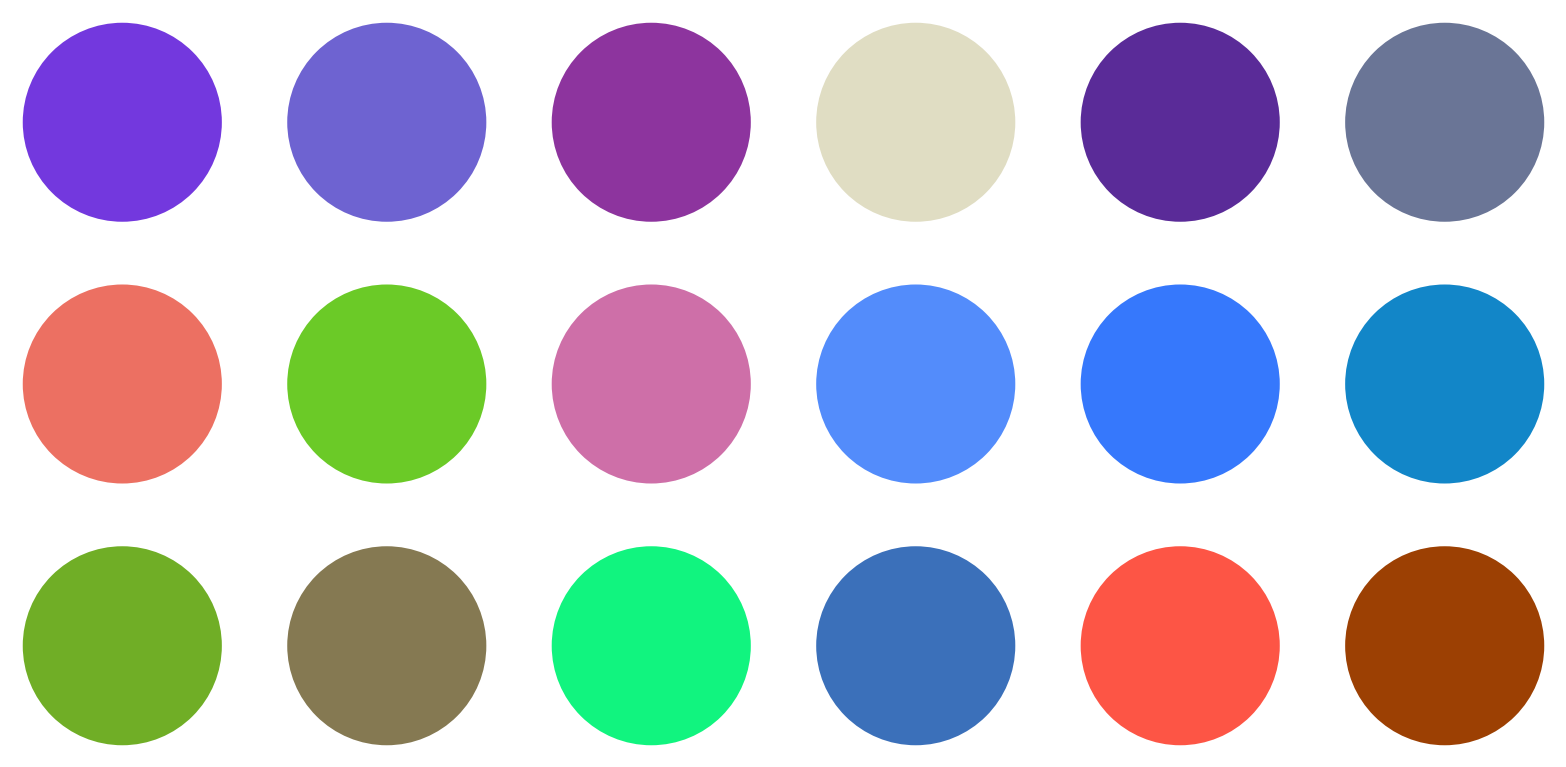
| Sample expected output: |  
  | -Graphics- |

Genere un diagrama circular de los PIB (GDP en inglés) de los países miembros del G5, con cada sector etiquetado. »

| Sample expected output: |  
  | -Graphics- |

Dibuje un diagrama circular de las poblaciones de los países miembros del G5 con una leyenda para cada sector. »

| Sample expected output: |  
  | -Graphics- |

Construya un GraphicsGrid de 5×5 con los sectores circulares que dan las frecuencias relativas de los dígitos de 2^n, con n a partir de 1. »

| Expected output: |  
  | -Graphics- |

Construya una fila de gráficos de la nube de palabras para los artículos de Wikipedia sobre cada uno de los países miembros del G5. »

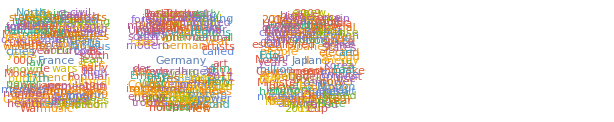
| Sample expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Se pueden redondear las esquinas en Framed?

Sí. Hay que usar la opción RoundingRadius→0.2, por ejemplo.

¿Qué tipo de cosas se pueden poner en una etiqueta?

Cualquier cosa que se desee. Puede ser texto, una gráfico o, incluso, un cuaderno completo.

¿Puede usarse Labeled para poner etiquetas en otras partes, además de en la parte inferior?

Sí. Puede usarse, por ejemplo, Labeled[expr,label,Left] o Labeled[expr,label,Right].

¿Cómo se determina dónde va una leyenda?

Use Placed.

La visualización, ¿puede ser animada o dinámica?

Sí. ListAnimate crea una animación. Hay muchas posibilidades, desde Tooltip hasta Manipulate, para construir visualizaciones dinámicas.

Notas técnicas

Wolfram Language busca colocar las etiquetas de manera que no interfieran con los datos que se grafican.

Se puede redimensionar cualquier gráfica usando Show[gráfica,ImageSize→ancho] o Show[gráfica,ImageSize→{ancho,alto}]. ImageSize→Tiny, etc. también funcionan.

PlotTheme→"BlackBackground" puede ser útil para personas con visión disminuida. PlotTheme→"Monochrome" evita el uso de colores.

ListPlot, PieChart, etc. trabajan con asociaciones (<|...|>) automáticamente, tomando las claves como coordenadas cuando sea lo apropiado y, cuando no, tratándolas como anotaciones.

Hay muchos tipos de leyendas diferentes: LineLegend, BarLegend, etc.

Para explorar más

Guía para poner etiquetas y anotaciones en Wolfram Language »